I heard about Stephen Wolfram, when I came across a video of his discussion with one of my other favorite scientists Nassim Taleb.

In New Kind of Science, Stephen Wolfram started to fill this gap, with his study of tissue growth and pigmentation patterns.

and in the past year or so, Stephen Wolfram has filled this gap and pioneered some groundbreaking computational models for biological systems. Starting as a fan of the research, and eventually becoming a collaborator, I’ve become convinced that we’ve struck gold and are now in a position to understand the high-level features of biology better than ever before.

In exploring Stephen Wolfram’s perspective on biology,

In my opinion, Stephen Wolfram is one of the most prolific scientists of our time. His Magnum Opus, New Kind of Science, is one of my favorite books ever, and the tool he created for doing science.

Interestingly, he didn’t (and still doesn’t) make his money off of science. Now, you may have noticed that I make my money from his institute

In the current paradigm, the obvious question is, “What about machine learning?”. We will definitely come back to this in his more recent work.  This claim as we’ll see, is a point of contention within Stephen’s work, and in his more recent work he essentially goes the other way.

```mathematica
Module[{
k=3,r=1,cut=200,deep=5000,fun=Length,
init,evo,ru,data,lt,test,mask,canonical,res},
res=ParallelTable[SeedRandom[seed];
init=FromDigits[Lookup[Association[Thread[Append[
Permutations[CenterArray[1,2r+1]],
CenterArray[0,2r+1]]->1]],{{"[◼]", "RuleTuples"}}[k,r],0],2];
init={0,{0,init},1,fun[{{1}}]};
evo=NestList[Function[item,
ru=First[{{"[◼]", "RandomRuleMutation"}}[{First[item],k,r}]];
data=CellularAutomaton[{ru,k,r},{{1},0},{cut,All}];
lt=If[SameQ[#,0],True,cut-#+1]&[
LengthWhile[Reverse[data],Total[#]==0&]];
If[TrueQ[lt],item,
test=fun[{{"[◼]", "MatrixCrop"}}[data]];
If[test<Last[item],item,
data=Union[Catenate[Partition[#,2r+1,1]&/@data]];
mask=Lookup[Association[Thread[data->1]],{{"[◼]", "RuleTuples"}}[k,r],0];
canonical=IntegerDigits[ru,k,k^(2r+1)];
canonical={FromDigits[canonical*mask,k],
FromDigits[mask,2]};
{ru,canonical,lt,test}
]]],init,deep];
evo=Map[Rest@*First,SplitBy[evo,#[[2]]&]];
evo=Map[DeleteDuplicates,SplitBy[evo,Last]];
res=Map[CompoundExpression[
data=CellularAutomaton[{#[[1,1]],3,1},{{1},0},#[[2]]+2],
ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
ImageSize->{Automatic,20(Length[data]+1)^.7}]]&,
evo,{2}];
Map[First,res]
,
{seed,5000+{16,54,60}}];
GraphicsColumn[
Map[GraphicsRow,res]
]
]
```

-Graphics-

And again, in Wolfram's words, and I agree: “one can’t help but be struck by how ‘lifelike’ this all looks—both in the complexity of these patterns, and in their diversity.”

, and I do think we may be able 
these systems a

is happening based on some high-level metric, like length or width or aspect ratio, in our case. But the crucial fact, is that 

In other words, evolution is like a  computationally-bounded observer of organisms. And because biological systems are capable of arbitrarily complex behavior,  the mechanisms that will be found by evolution will be full of irreducibility.

And this phenomenon that adaptively evolved patterns tends to use irreducibility mechanisms to achieve their goals, Stephen finds, is quite general.

Not only that but in running these algorithms we get these so-called “idealized organisms” that we can study as a model for biological organisms. 

 And as we saw in the case of rule 30, making something visually concrete can be a complete difference-maker. So before we even get to specific conclusions, this is already somewhat of a breakthrough.

Randomness, for example, is usually injected artificially into

But what are the claims, what can we say about biological systems from this model?

The most obvious claim is the sheer complexity of the resulting patterns that we get. It’s not clear where the pattern

The most striking thing about this model, is its simplicity and explainability (I was able to explain with a few sentences and pictures) and

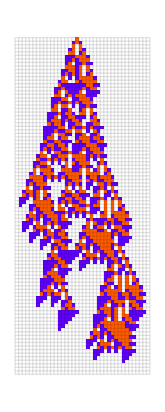

```mathematica
With[{ru={6006804516645,3,1}},GraphicsRow[
{RulePlot[CellularAutomaton[ru],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
MeshStyle->Opacity[.2],ImageSize->280],ArrayPlot[ArrayPad[CellularAutomaton[ru,{{1},0},94],{{0,0},{1,1}}],
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
Mesh->True,MeshStyle->Opacity[.1],ImageSize->{165,Automatic}]},Spacings->40]]
```

```mathematica
RandomChoice[{0,1,2,3},{15,4^(2*1+1)-1}]
```

```mathematica
SeedRandom[123];
rule=ResourceFunction["RandomCA"][{2}]
```

Namely, he did a thorough exploration of evolution and biological systems from the perspective of these adapted cellular automata. 


 First he looked at evolution, then he branched out, looking at medicine from the perspective of these idealized organisms.

The first and arguably most important role of

that started from a single black cell and went to an all-white state at step 50, by changing one rule at a time. And surprisingly, it worked:

Th he started to get a sense for how these adaptive processes work (with Richard Assar). That, in combination with thinking

This idea, of

It basically came from his intuition with Richard Assar

Now, I have to say, I am still not sold on this point. Obviously, and I’ve had this discussion with Stephen, there is some amount of reducibility in biological organisms (we are made up of cells, and have different organs etc.) but It’s really a question of how much, and I think that’s a question that needs to be explored further. We have some experiments that I believe really get at this question, which I will discuss later.

But there’s no doubt that within biology, there is often a vague assumption that everything in the end can be explained, we just need to do more experiments and drill down to lower-levels. And Stephen’s point, and what this model shows, is that at some point, you reach a limit for how much of biological systems you can actually explain.

This difference is something I’ve discusses with Stephen, and that we both agree is an important distinction.

But okay, what were some biological applications to Stephen’s newfound realization that complexity is abundant?

But going even further, and Stephen makes a point of this, evolution, because it has this problem of getting stuck in complex landscapes, rather than making things more complex, has the effect of making things simpler. 

The idea being that for simpler systems, it is easier to “push them” up some fitness hill, suggesting that evolution would “prefer” simpler systems.

And Stephen then makes the, in many ways radical claim

These claims about adaptive algorithms and the effects of natural selection, are something that Stephen reexamines thoroughly in his recent work on biology and machine learning, and it’s something we’ll come back to in then next section.

I should note that this distinction is really the same as the distinction between evolutionary and developmental biology. And most of Wolfram’s models in New Kind of Science are on the side of developmental biology. Importantly for us, this has changed in his recent work, where he had a breakthrough in using cellular automata to model evolution, which we’ll discuss in the next section. 

But clearly, both evolution and physical constraints are contributing to what’s observed in biology, and it’s really a question of how much to attribute to either side. What Stephen is saying in NKS, and what he still maintains with his new work, is that the field of biology tends to attribute too much of the observed behaviors to evolution, and not enough to the physical behaviors of the system.

And the key discovery of NKS, is these “wildly-behaved” programs, are quite easy to find. Stephen then uses that idea to claim that developmental biology is a more

And this is basically like the distinction between evolutionary and developmental biology.

And this new model, in many ways, extends and concretizes the claims from NKS. Namely, not only are the behavior of certain processes like pigmentation and leaf shape a consequence of small changes in simple programs

Namely, that any adaptive system, including biolo

, in many ways, makes concrete the claims of NKS, that 

, that biological processes are full of irreducibilu

Now this claim is fundamentally different to the claim made about evolution in New Kind of Science. This difference is something I’ve asked Stephen about, and I believe is an important distinction.

In NKS, Stephen did not have a such a clear model for evolution, and the systems that it produces. While he did start to get at it with the constraint-satisfaction problems, that model did not produce a clear “idealized organism” of the kind that the new model produces.

And because of that, he couldn’t paint a concise picture for the level of irreducibility in biological processes. So the conclusion from NKS, was basically that non-essential processes like pigmentation, are full of irreducibility, but the functioning of essential processes, like the organ systems for instance, are largely pretty simple. And their simplicity is what enables them to be shaped by evolution.

But with this new work, Stephen is now claiming that even the essential processes, like the functioning of organs, are full of irreducibility.

Now importantly, and I’ve asked Stephen about this, this claim is, in a way, the opposite of Stephen’s claim about evolution in New Kind of Science. 

So let’s break down the differences.

And in discussing this with Stephen, he basically said that in NKS, he didn’t have a clear model for evolution. 

you may be thinking, doesn’t this contradict the claim that Stephen made in New Kind of Science that evolution has a simplifying effect. And

Now, I have to say, I am still not sold on this point. Obviously, and I’ve had this discussion with Stephen, there is some amount of reducibility in biological organisms (we are made up of cells, and have different organs etc.) but It’s really a question of how much, and I think that’s a question that needs to be explored further. We have some experiments that I believe really get at this question, which I will discuss later.

But there’s no doubt that within biology, there is often a vague assumption that everything in the end can be explained, we just need to do more experiments and drill down to lower-levels. And Stephen’s point, and what this model shows, is that at some point, you reach a limit for how much of biological systems you can actually explain.

While I think the exact takeaways from these models are subject to change, I do believe that we are having a bit of a “rule 30 moment”.

In the past, we did not have such a simple model for an adapted system.

I think at this point it is clear that Stephen has laid down some powerful foundational models for thinking about biology. But the big question is where can we go with these ideas, both within biology and beyond.

And it is now my mission, to try to help make that happen. A

And I hope in hearing t

Right now, our biology effort at the Wolfram Institute is still not well-funded, and we’re actually looking for a pHD-level theoretical biologist to help us. So funnily enough, right now, it’s really just me working on these things.

I’m particularly interested in exploring these ideas in the context of computer security, the science of aging, behavior analysis, immunology

And in many ways this is already happening.

But again, regardless of

is that in general is that many phenomena in medicine, like

Stephen has also explored in-depth the idea of using these adapted cellular automata as a model for an organism, then 

 using perturbations to the cells of the automata as a model for uncertain changes in the environment, and then studying the resulting patterns as models of disease and treatment. I actually worked on this with him, and I believe it has potentially important implications for medicine, so I think

And I think just going through the references and exploring what’s interesting to you is also a reasonable approach.